# Problem 11.7

```mathematica
deltax=5*10^-6;
h=2*deltax;
lambda=500*10^-9;
z=1;
```

```mathematica
Intensity[n_]:=(Sinc[Pi*deltax/(lambda*z)*x])^2*(Sin[n*Pi*h*x/(lambda*z)])^2/(n^2*(Sin[Pi*h*x/(lambda*z)])^2)
```

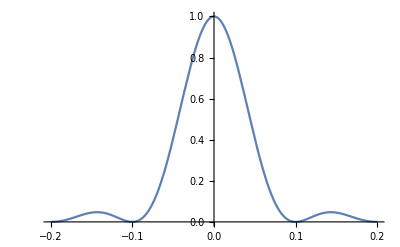

```mathematica
Plot[Intensity[1],{x,-0.2,0.2},PlotRange->All]
```

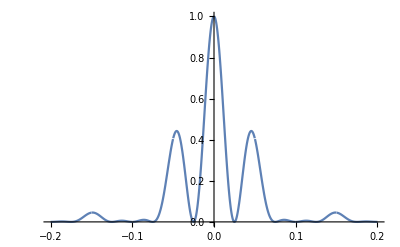

```mathematica
Plot[Intensity[2],{x,-0.2,0.2},PlotRange->All]
```

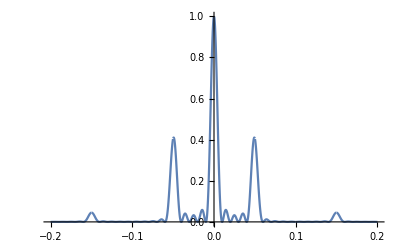

```mathematica
Plot[Intensity[5],{x,-0.2,0.2},PlotRange->All]
```

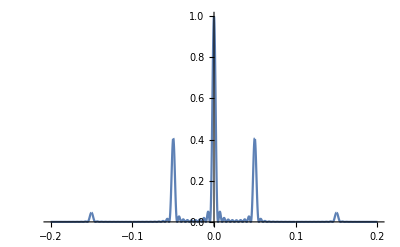

```mathematica
Plot[Intensity[10],{x,-0.2,0.2},PlotRange->All]
```

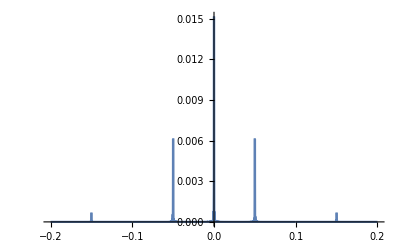

```mathematica
Plot[Intensity[1000],{x,-0.2,0.2},PlotRange->All]
```

I do not expect the I_peak to be the same. The N = 1000 is a lot different.